```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]<>"../"];
Needs["ThinLayer`","ThinLayer.m"]
FigExportPath=NotebookDirectory[]<>"../../../../Publications_and_conferences/Conferences/EAGE-2019/Presentation/Fig/"
```

/Users/ymac/Dropbox/Study_etc/NTNU/Anisotropy/Mathematica/PETROMAKS/PM2-codes-EAGE-19/EAGE'19/../../../../Publications_and_conferences/Conferences/EAGE-2019/Presentation/Fig/

## Rock physics model

```mathematica
(*Get Phase/Group velocities + group angle*)
vVβ[c_,Α_]:=Module[{c11=c[[1]],c13=c[[2]],c33=c[[3]],c44=c[[4]],a,b,da,db,vP2,vS2,vP,vS,VP,VS,dvP,dvS,βP,βS,α},
α=Α Pi/180;

a=1/4 (c33+2 c44+c33 Cos[2 α]+2 c11 Sin[α]^2);
b=1/2 √(-4 c33 c44 Cos[α]^4+1/4 (c11+c33+2 c44+(-c11+c33) Cos[2 α])^2-4 c11 c44 Sin[α]^4+(c13^2-c11 c33+2 c13 c44) Sin[2 α]^2);
da=(c11-c33) Cos[α] Sin[α];
db=((c11-c33) (c11+c33-2 c44) Sin[2 α]-1/2 (c11+2 c13+c33) (c11-2 c13+c33-4 c44) Sin[4 α])/(√2 √(3 c11^2+4 c13^2+3 c33^2-4 c33 c44+8 c44 (c13+c44)-2 c11 (c33+2 c44)-4 (c11-c33) (c11+c33-2 c44) Cos[2 α]+(c11+2 c13+c33) (c11-2 c13+c33-4 c44) Cos[4 α]));

vP2=a+b;
vS2=a-b;
vP=√vP2;
vS=√vS2;

dvP=(da+db)/(2 √(a+b));
dvS=(da-db)/(2 √(a-b));


VP=√(vP2+dvP^2);
VS=√(vS2+dvS^2);

βP=ArcTan[(1-dvP Tan[α]/vP),(Tan[α]+dvP/vP)]180/Pi;
βS=ArcTan[(1-dvS Tan[α]/vS),(Tan[α]+dvS/vS)]180/Pi;

{{vP,VP,βP},{vS,VS,βS}}
]
```

```mathematica
Module[{λ=10.6957 ,μ=21.9734 ,ρ2=2.15,ϕ=.28,kf=2.4,ϵ=0.02,ϵf=0.03,α=10^-5,τ=2. 10^-5,cijPorous,cijFractured,
thick=.005,is=600,fs=20},
cijPorous[f_]:=tlVTISquirtModuli[ϵ,0,α,τ,2Pi f,0][λ,μ,ρ2,ϕ,kf];
cijFractured[f_,lenrat_]:=tlVTISquirtModuli[ϵ,ϵf,α,τ,2Pi f,lenrat][λ,μ,ρ2,ϕ,kf];

vel={{
Show[
Plot[Evaluate@Re[{√((#[[1]])/(#[[5]])),√((#[[3]])/(#[[5]]))}&@cijPorous[10^f]],{f,0,5},PlotRange->{Full,{2.78,3.51}},ImageSize->is,Frame->True,PlotStyle->(Directive[#,Thickness[thick],Black]&/@{None,Dashed}),GridLines->Automatic,FrameLabel->{{"V, km/s",None},{"Log f, Hz","qP Velocity dispersion @ 0, 90°"}},LabelStyle->Directive[Black,Bold,FontSize->fs]],
Plot[Evaluate@Re[{√((#[[1]])/(#[[5]])),√((#[[3]])/(#[[5]]))}&@cijFractured[10^f,100]],{f,0,5},PlotRange->{Full,Full},PlotStyle->(Directive[#,Red,Thickness[thick]]&/@{None,Dashed})],
Plot[Evaluate@Re[{√((#[[1]])/(#[[5]])),√((#[[3]])/(#[[5]]))}&@cijFractured[10^f,200]],{f,0,5},PlotRange->{Full,Full},PlotStyle->(Directive[#,Cyan,Thickness[thick]]&/@{None,Dashed})],
Plot[Evaluate@Re[{√((#[[1]])/(#[[5]])),√((#[[3]])/(#[[5]]))}&@cijFractured[10^f,300]],{f,0,5},PlotRange->{Full,Full},PlotStyle->(Directive[#,Magenta,Thickness[thick]]&/@{None,Dashed})]
],
Show[
Plot[Evaluate@Re[√((#[[4]])/(#[[5]]))&@cijPorous[10^f]],{f,0,5},PlotRange->{Full,{1.8,2.06}},ImageSize->is,Frame->True,PlotStyle->(Directive[#,Thick]&/@{Black}),GridLines->Automatic,FrameLabel->{{"V, km/s",None},{"Log f, Hz","qS Velocity dispersion @ 0, 90°"}},LabelStyle->Directive[Black,Bold,FontSize->fs]],
Plot[Evaluate@Re[√((#[[4]])/(#[[5]]))&@cijFractured[10^f,100]],{f,0,5},PlotRange->{Full,Full},PlotStyle->(Directive[#,Red,Thickness[thick]]&/@{Dashed})],
Plot[Evaluate@Re[√((#[[4]])/(#[[5]]))&@cijFractured[10^f,200]],{f,0,5},PlotRange->{Full,Full},PlotStyle->(Directive[#,Cyan,Thickness[thick]]&/@{Dashed})],
Plot[Evaluate@Re[√((#[[4]])/(#[[5]]))&@cijFractured[10^f,500]],{f,0,5},PlotRange->{Full,Full},PlotStyle->(Directive[#,Magenta,Thickness[thick]]&/@{Dashed})]
]}};

Q={{
Show[
Plot[Evaluate[{(Abs@Im@#[[1]])/(Re@#[[1]]),(Abs@Im@#[[3]])/(Re@#[[3]])}&@cijPorous[10^f]],{f,0,5},PlotRange->{Full,{0,.22}},ImageSize->is,Frame->True,PlotStyle->(Directive[#,Black,Thickness[thick]]&/@{None,Dashed}),GridLines->Automatic,FrameLabel->{{"1/Q",None},{"Log f, Hz","qP attenuation @ 0, 90°"}},LabelStyle->Directive[Black,Bold,FontSize->fs]],
Plot[Evaluate[{(Abs@Im@#[[1]])/(Re@#[[1]]),(Abs@Im@#[[3]])/(Re@#[[3]])}&@cijFractured[10^f,100]],{f,0,5},PlotRange->{Full,Full},PlotStyle->(Directive[#,Red,Thickness[thick]]&/@{None,Dashed})],
Plot[Evaluate[{(Abs@Im@#[[1]])/(Re@#[[1]]),(Abs@Im@#[[3]])/(Re@#[[3]])}&@cijFractured[10^f,200]],{f,0,5},PlotRange->{Full,Full},PlotStyle->(Directive[#,Cyan,Thickness[thick]]&/@{None,Dashed})],
Plot[Evaluate[{(Abs@Im@#[[1]])/(Re@#[[1]]),(Abs@Im@#[[3]])/(Re@#[[3]])}&@cijFractured[10^f,300]],{f,0,5},PlotRange->{Full,Full},PlotStyle->(Directive[#,Magenta,Thickness[thick]]&/@{None,Dashed})]
],
Show[
Plot[Evaluate[(Abs@Im@#[[4]])/(Re@#[[4]])&@cijPorous[10^f]],{f,0,5},PlotRange->{Full,{0,.09}},ImageSize->is,Frame->True,PlotStyle->(Directive[#,Thickness[thick]]&/@{Black}),GridLines->Automatic,FrameLabel->{{"1/Q",None},{"Log f, Hz","qS attenuation @ 0, 90°"}},LabelStyle->Directive[Black,Bold,FontSize->fs]],
Plot[Evaluate[(Abs@Im@#[[4]])/(Re@#[[4]])&@cijFractured[10^f,100]],{f,0,5},PlotRange->{Full,Full},PlotStyle->(Directive[#,Red,Thickness[thick]]&/@{None})],
Plot[Evaluate[(Abs@Im@#[[4]])/(Re@#[[4]])&@cijFractured[10^f,200]],{f,0,5},PlotRange->{Full,Full},PlotStyle->(Directive[#,Cyan,Thickness[thick]]&/@{None})],
Plot[Evaluate[(Abs@Im@#[[4]])/(Re@#[[4]])&@cijFractured[10^f,300]],{f,0,5},PlotRange->{Full,Full},PlotStyle->(Directive[#,Magenta,Thickness[thick]]&/@{None})]
]}};
]
```

```mathematica
With[{format=".eps"},
Table[Export[FigExportPath<>"vel-"<>Switch[i,1,"P",2,"S"]<>format,vel[[1,i]]],{i,2}];
Table[Export[FigExportPath<>"q-"<>Switch[i,1,"P",2,"S"]<>format,Q[[1,i]]],{i,2}];
]
```

```mathematica
vel//TableForm
Q//TableForm
```

```mathematica
θlist={15,30,45,60};
velθ={};
Qθ={};
Table[
Module[{λ=10.6957 ,μ=21.9734 ,ρ2=2.15,ϕ=.28,kf=2.4,ϵ=0.02,ϵf=0.03,α=10^-5,τ=2. 10^-5,cijPorous,cijFractured,
thick=.005,is=600,fs=20,θ=angle},

cijPorous[f_]:=tlVTISquirtModuli[ϵ,0,α,τ,2Pi f,0][λ,μ,ρ2,ϕ,kf];
cijFractured[f_,lenrat_]:=tlVTISquirtModuli[ϵ,ϵf,α,τ,2Pi f,lenrat][λ,μ,ρ2,ϕ,kf];

AppendTo[velθ,{{
Show[
Plot[Evaluate@Re[{√((#[[1]])/(#[[5]])),√((#[[3]])/(#[[5]]))}&@cijPorous[10^f]],{f,0,5},PlotRange->{Full,{2.78,3.51}},ImageSize->is,Frame->True,PlotStyle->(Directive[#,Thickness[thick],Black]&/@{None,Dashed}),GridLines->Automatic,FrameLabel->{{"V, km/s",None},{"Log f, Hz","qP Velocity dispersion @ "<>ToString[θ]<>"°"}},LabelStyle->Directive[Black,Bold,FontSize->fs]],
Plot[Evaluate@Re[{√((#[[1]])/(#[[5]])),√((#[[3]])/(#[[5]]))}&@cijFractured[10^f,100]],{f,0,5},PlotRange->{Full,Full},PlotStyle->(Directive[#,Red,Thickness[thick]]&/@{None,Dashed})],
Plot[Evaluate@Re[{√((#[[1]])/(#[[5]])),√((#[[3]])/(#[[5]]))}&@cijFractured[10^f,200]],{f,0,5},PlotRange->{Full,Full},PlotStyle->(Directive[#,Cyan,Thickness[thick]]&/@{None,Dashed})],
Plot[Evaluate@Re[{√((#[[1]])/(#[[5]])),√((#[[3]])/(#[[5]]))}&@cijFractured[10^f,300]],{f,0,5},PlotRange->{Full,Full},PlotStyle->(Directive[#,Magenta,Thickness[thick]]&/@{None,Dashed})],
Plot[Evaluate@Re[vVβ[cijFractured[10^f,100],θ][[1,2]]/√ρ2],{f,0,5},PlotRange->{Full,Full},PlotStyle->(Directive[#,Red,Thickness[thick]]&/@{None,Dotted})],
Plot[Evaluate@Re[vVβ[cijFractured[10^f,200],θ][[1,2]]/√ρ2],{f,0,5},PlotRange->{Full,Full},PlotStyle->(Directive[#,Cyan,Thickness[thick]]&/@{None,Dotted})],
Plot[Evaluate@Re[vVβ[cijFractured[10^f,300],θ][[1,2]]/√ρ2],{f,0,5},PlotRange->{Full,Full},PlotStyle->(Directive[#,Magenta,Thickness[thick]]&/@{None,Dotted})]
],
Show[
Plot[Evaluate@Re[√((#[[4]])/(#[[5]]))&@cijPorous[10^f]],{f,0,5},PlotRange->{Full,{1.8,2.06}},ImageSize->is,Frame->True,PlotStyle->(Directive[#,Thick]&/@{Black}),GridLines->Automatic,FrameLabel->{{"V, km/s",None},{"Log f, Hz","qS Velocity dispersion @ "<>ToString[θ]<>"°"}},LabelStyle->Directive[Black,Bold,FontSize->fs]],
Plot[Evaluate@Re[√((#[[4]])/(#[[5]]))&@cijFractured[10^f,100]],{f,0,5},PlotRange->{Full,Full},PlotStyle->(Directive[#,Red,Thickness[thick]]&/@{Dashed})],
Plot[Evaluate@Re[√((#[[4]])/(#[[5]]))&@cijFractured[10^f,200]],{f,0,5},PlotRange->{Full,Full},PlotStyle->(Directive[#,Cyan,Thickness[thick]]&/@{Dashed})],
Plot[Evaluate@Re[√((#[[4]])/(#[[5]]))&@cijFractured[10^f,500]],{f,0,5},PlotRange->{Full,Full},PlotStyle->(Directive[#,Magenta,Thickness[thick]]&/@{Dashed})],
Plot[Evaluate@Re[vVβ[cijFractured[10^f,100],θ][[2,2]]/√ρ2],{f,0,5},PlotRange->{Full,Full},PlotStyle->(Directive[#,Red,Thickness[thick]]&/@{Dotted})],
Plot[Evaluate@Re[vVβ[cijFractured[10^f,200],θ][[2,2]]/√ρ2],{f,0,5},PlotRange->{Full,Full},PlotStyle->(Directive[#,Cyan,Thickness[thick]]&/@{Dotted})],
Plot[Evaluate@Re[vVβ[cijFractured[10^f,300],θ][[2,2]]/√ρ2],{f,0,5},PlotRange->{Full,Full},PlotStyle->(Directive[#,Magenta,Thickness[thick]]&/@{Dotted})]
]}}];

AppendTo[Qθ,{{
Show[
Plot[Evaluate[{(Abs@Im@#[[1]])/(Re@#[[1]]),(Abs@Im@#[[3]])/(Re@#[[3]])}&@cijPorous[10^f]],{f,0,5},PlotRange->{Full,{0,.22}},ImageSize->is,Frame->True,PlotStyle->(Directive[#,Black,Thickness[thick]]&/@{None,Dashed}),GridLines->Automatic,FrameLabel->{{"1/Q",None},{"Log f, Hz","qP attenuation @ "<>ToString[θ]<>"°"}},LabelStyle->Directive[Black,Bold,FontSize->fs]],
Plot[Evaluate[{(Abs@Im@#[[1]])/(Re@#[[1]]),(Abs@Im@#[[3]])/(Re@#[[3]])}&@cijFractured[10^f,100]],{f,0,5},PlotRange->{Full,Full},PlotStyle->(Directive[#,Red,Thickness[thick]]&/@{None,Dashed})],
Plot[Evaluate[{(Abs@Im@#[[1]])/(Re@#[[1]]),(Abs@Im@#[[3]])/(Re@#[[3]])}&@cijFractured[10^f,200]],{f,0,5},PlotRange->{Full,Full},PlotStyle->(Directive[#,Cyan,Thickness[thick]]&/@{None,Dashed})],
Plot[Evaluate[{(Abs@Im@#[[1]])/(Re@#[[1]]),(Abs@Im@#[[3]])/(Re@#[[3]])}&@cijFractured[10^f,300]],{f,0,5},PlotRange->{Full,Full},PlotStyle->(Directive[#,Magenta,Thickness[thick]]&/@{None,Dashed})],

Plot[Evaluate[(Abs@Im[#^2])/(Re@Re[#^2])&@vVβ[cijFractured[10^f,100],θ][[1,1]]],{f,0,5},PlotRange->{Full,Full},PlotStyle->(Directive[#,Red,Thickness[thick]]&/@{None,Dotted})],
Plot[Evaluate[(Abs@Im[#^2])/(Re@Re[#^2])&@vVβ[cijFractured[10^f,200],θ][[1,1]]],{f,0,5},PlotRange->{Full,Full},PlotStyle->(Directive[#,Cyan,Thickness[thick]]&/@{None,Dotted})],
Plot[Evaluate[(Abs@Im[#^2])/(Re@Re[#^2])&@vVβ[cijFractured[10^f,300],θ][[1,1]]],{f,0,5},PlotRange->{Full,Full},PlotStyle->(Directive[#,Magenta,Thickness[thick]]&/@{None,Dotted})]
],
Show[
Plot[Evaluate[(Abs@Im@#[[4]])/(Re@#[[4]])&@cijPorous[10^f]],{f,0,5},PlotRange->{Full,{0,.09}},ImageSize->is,Frame->True,PlotStyle->(Directive[#,Thickness[thick]]&/@{Black}),GridLines->Automatic,FrameLabel->{{"1/Q",None},{"Log f, Hz","qS attenuation @ "<>ToString[θ]<>"°"}},LabelStyle->Directive[Black,Bold,FontSize->fs]],
Plot[Evaluate[(Abs@Im@#[[4]])/(Re@#[[4]])&@cijFractured[10^f,100]],{f,0,5},PlotRange->{Full,Full},PlotStyle->(Directive[#,Red,Thickness[thick]]&/@{None})],
Plot[Evaluate[(Abs@Im@#[[4]])/(Re@#[[4]])&@cijFractured[10^f,200]],{f,0,5},PlotRange->{Full,Full},PlotStyle->(Directive[#,Cyan,Thickness[thick]]&/@{None})],
Plot[Evaluate[(Abs@Im@#[[4]])/(Re@#[[4]])&@cijFractured[10^f,300]],{f,0,5},PlotRange->{Full,Full},PlotStyle->(Directive[#,Magenta,Thickness[thick]]&/@{None})],

Plot[Evaluate[(Abs@Im[#^2])/(Re@Re[#^2])&@vVβ[cijFractured[10^f,100],θ][[2,1]]],{f,0,5},PlotRange->{Full,Full},PlotStyle->(Directive[#,Red,Thickness[thick]]&/@{None,Dotted})],
Plot[Evaluate[(Abs@Im[#^2])/(Re@Re[#^2])&@vVβ[cijFractured[10^f,200],θ][[2,1]]],{f,0,5},PlotRange->{Full,Full},PlotStyle->(Directive[#,Cyan,Thickness[thick]]&/@{None,Dotted})],
Plot[Evaluate[(Abs@Im[#^2])/(Re@Re[#^2])&@vVβ[cijFractured[10^f,300],θ][[2,1]]],{f,0,5},PlotRange->{Full,Full},PlotStyle->(Directive[#,Magenta,Thickness[thick]]&/@{None,Dotted})]
]}}];
],
{angle,θlist}
];
```

```mathematica
velθ//TableForm
Qθ//TableForm
```

```mathematica
With[{format=".eps"},
Table[
Table[Export[FigExportPath<>"vel-"<>Switch[i,1,"P",2,"S"]<>ToString[j]<>format,velθ[[j,1,i]]],{i,2}];
Table[Export[FigExportPath<>"q-"<>Switch[i,1,"P",2,"S"]<>ToString[j]<>format,Qθ[[j,1,i]]],{i,2}];
,{j,1,Dimensions[vel][[1]]}];
]
```

## Reflection response

```mathematica
(*Get Phase/Group velocities + group angle*)
vVβp[c_,Α_]:=Module[{c11=c[[1]],c13=c[[2]],c33=c[[3]],c44=c[[4]],a,b,da,db,vP2,vS2,vP,vS,VP,VS,dvP,dvS,βP,βS,α,pP,pS},
α=Α Pi/180;

a=1/4 (c33+2 c44+c33 Cos[2 α]+2 c11 Sin[α]^2);
b=1/2 √(-4 c33 c44 Cos[α]^4+1/4 (c11+c33+2 c44+(-c11+c33) Cos[2 α])^2-4 c11 c44 Sin[α]^4+(c13^2-c11 c33+2 c13 c44) Sin[2 α]^2);
da=(c11-c33) Cos[α] Sin[α];
db=((c11-c33) (c11+c33-2 c44) Sin[2 α]-1/2 (c11+2 c13+c33) (c11-2 c13+c33-4 c44) Sin[4 α])/(√2 √(3 c11^2+4 c13^2+3 c33^2-4 c33 c44+8 c44 (c13+c44)-2 c11 (c33+2 c44)-4 (c11-c33) (c11+c33-2 c44) Cos[2 α]+(c11+2 c13+c33) (c11-2 c13+c33-4 c44) Cos[4 α]));

vP2=a+b;
vS2=a-b;
vP=√vP2;
vS=√vS2;

dvP=(da+db)/(2 √(a+b));
dvS=(da-db)/(2 √(a-b));


VP=√(vP2+dvP^2);
VS=√(vS2+dvS^2);

βP=ArcTan[(1-dvP Tan[α]/vP),(Tan[α]+dvP/vP)]180/Pi;
βS=ArcTan[(1-dvS Tan[α]/vS),(Tan[α]+dvS/vS)]180/Pi;

pP=Sin[Α]/vP;
pS=Sin[Α]/vS;

{{vP,pP,VP,βP},{vS,pS,VS,βS}}
]
```

```mathematica
setlayer[ω_,lenrat_]:=Module[
{λ=10.6957 ,μ=21.9734 ,ρ2=2.15,ϕ=.28,kf=2.4,ϵ=0.02,ϵf=0.03,α=10^-5,τ=2. 10^-5,cijPorous,cijFractured},
cijPorous=tlVTISquirtModuli[ϵ,0,α,τ,ω,0][λ,μ,ρ2,ϕ,kf];
cijFractured=tlVTISquirtModuli[ϵ,ϵf,α,τ,ω,lenrat][λ,μ,ρ2,ϕ,kf];
tlSetLayer[1,cijPorous];
tlSetLayer[2,cijFractured];
]
```

```mathematica
rr[p_,f_,l_]:=Module[{},
setlayer[2Pi f,l];
tlReflectivity[{1,2},{0,0},p,2Pi f]
]
```

```mathematica
vIso[i_Integer]:=√((#[[1]])/(#[[5]])&@tlGetStiffness[i])
```

```mathematica
(*RE*)
Table[
Module[{f=f0},
rPP=Show[
ParametricPlot[{
{α,Re@rr[Sin[α Pi/180]/vIso[1],f,100][[1,1]]},
{α,Re@rr[Sin[α Pi/180]/vIso[1],f,200][[1,1]]},
{α,Re@rr[Sin[α Pi/180]/vIso[1],f,300][[1,1]]}
}
,
{α,0,90},AspectRatio->1,PlotRange->{Full,{-0.07,0.2}},ImageSize->600,Frame->True,PlotStyle->(Directive[#,Thickness[.005]]&/@{Red,Cyan,Magenta}),GridLines->Automatic,FrameLabel->{{"R",None},{"θ, °","PP-reflection coefficient @ "<>ToString[f]<>" Hz"}},LabelStyle->Directive[Black,Bold,FontSize->20]],
ParametricPlot[{
{α,Im@rr[Sin[α Pi/180]/vIso[1],f,100][[1,1]]},
{α,Im@rr[Sin[α Pi/180]/vIso[1],f,200][[1,1]]},
{α,Im@rr[Sin[α Pi/180]/vIso[1],f,300][[1,1]]}
}
,
{α,0,90},PlotStyle->(Directive[#,Dashed,Thickness[.005]]&/@{Red,Cyan,Magenta})]
];

rPS=Show[
ParametricPlot[{
{α,Re@rr[Sin[α Pi/180]/vIso[1],f,100][[1,2]]},
{α,Re@rr[Sin[α Pi/180]/vIso[1],f,200][[1,2]]},
{α,Re@rr[Sin[α Pi/180]/vIso[1],f,300][[1,2]]}
}
,
{α,0,90},AspectRatio->1,PlotRange->{Full,{0,.08}},ImageSize->600,Frame->True,PlotStyle->(Directive[#,Thickness[.005]]&/@{Red,Cyan,Magenta}),GridLines->Automatic,FrameLabel->{{"R",None},{"θ, °","PS-reflection coefficient @ "<>ToString[f]<>" Hz"}},LabelStyle->Directive[Black,Bold,FontSize->20]],
ParametricPlot[{
{α,Im@rr[Sin[α Pi/180]/vIso[1],f,100][[1,2]]},
{α,Im@rr[Sin[α Pi/180]/vIso[1],f,200][[1,2]]},
{α,Im@rr[Sin[α Pi/180]/vIso[1],f,300][[1,2]]}
}
,
{α,0,90},PlotStyle->(Directive[#,Dashed,Thickness[.005]]&/@{Red,Cyan,Magenta})]
];

rSS=Show[
ParametricPlot[{
{α,Re@rr[Sin[α Pi/180]/vIso[1],f,100][[2,2]]},
{α,Re@rr[Sin[α Pi/180]/vIso[1],f,200][[2,2]]},
{α,Re@rr[Sin[α Pi/180]/vIso[1],f,300][[2,2]]}
}
,
{α,0,90},AspectRatio->1,PlotRange->{Full,{-.06,.07}},ImageSize->600,Frame->True,PlotStyle->(Directive[#,Thickness[.005]]&/@{Red,Cyan,Magenta}),GridLines->Automatic,FrameLabel->{{"R",None},{"θ, °","SS-reflection coefficient @ "<>ToString[f]<>" Hz"}},LabelStyle->Directive[Black,Bold,FontSize->20]],
ParametricPlot[{
{α,Im@rr[Sin[α Pi/180]/vIso[1],f,100][[2,2]]},
{α,Im@rr[Sin[α Pi/180]/vIso[1],f,200][[2,2]]},
{α,Im@rr[Sin[α Pi/180]/vIso[1],f,300][[2,2]]}
}
,
{α,0,90},PlotStyle->(Directive[#,Dashed,Thickness[.005]]&/@{Red,Cyan,Magenta})]
];
r={rPP,rPS,rSS};

With[{format=".eps"},
Table[Export[FigExportPath<>"r"<>Switch[i,1,"PP",2,"PS",3,"SS"]<>ToString[f]<>format,r[[i]]],{i,3}];
]
],{f0,{20,40,60}}]
```

{Null,Null,Null}

```mathematica
(*STACK*)
rrr[p_,f_,l_]:=Module[{},
setlayer[2Pi f,l];
tlReflectivity[{1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1},{0.,0.00980392156862745,0.00980392156862745,0.00980392156862745,0.00980392156862745,0.00980392156862745,0.00980392156862745,0.00980392156862745,0.00980392156862745,0.00980392156862745,0.00980392156862745,0.00980392156862745,0.00980392156862745,0.00980392156862745,0.00980392156862745,0.00980392156862745,0.00980392156862745,0.00980392156862745,0.00980392156862745,0.00980392156862745,0.00980392156862745,0.00980392156862745,0.00980392156862745,0.00980392156862745,0.00980392156862745,0.00980392156862745,0.00980392156862745,0.00980392156862745,0.00980392156862745,0.00980392156862745,0.00980392156862745,0.00980392156862745,0.00980392156862745,0.00980392156862745,0.00980392156862745,0.00980392156862745,0.00980392156862745,0.00980392156862745,0.00980392156862745,0.00980392156862745,0.00980392156862745,0.00980392156862745,0.00980392156862745,0.00980392156862745,0.00980392156862745,0.00980392156862745,0.00980392156862745,0.00980392156862745,0.00980392156862745,0.00980392156862745,0.00980392156862745,0.00980392156862745,0.},p,2Pi f]
]
Module[{f=25},
rPP=ParametricPlot[{
{α,Re@rrr[Sin[α Pi/180]/vIso[1],f,100][[1,1]]},
{α,Re@rrr[Sin[α Pi/180]/vIso[1],f,200][[1,1]]},
{α,Re@rrr[Sin[α Pi/180]/vIso[1],f,300][[1,1]]}
}
,
{α,0,90},AspectRatio->1,PlotRange->{Full,{-0.055,0.065}},ImageSize->600,Frame->True,PlotStyle->(Directive[#,Thickness[.005]]&/@{Red,Cyan,Magenta}),GridLines->Automatic,FrameLabel->{{"R",None},{"θ, °","PP-reflectivity @ "<>ToString[f]<>" Hz"}},LabelStyle->Directive[Black,Bold,FontSize->20]];

rPS=ParametricPlot[{
{α,Re@rrr[Sin[α Pi/180]/vIso[1],f,100][[1,2]]},
{α,Re@rrr[Sin[α Pi/180]/vIso[1],f,200][[1,2]]},
{α,Re@rrr[Sin[α Pi/180]/vIso[1],f,300][[1,2]]}
}
,
{α,0,90},AspectRatio->1,PlotRange->{Full,Automatic},ImageSize->600,Frame->True,PlotStyle->(Directive[#,Thickness[.005]]&/@{Red,Cyan,Magenta}),GridLines->Automatic,FrameLabel->{{"R",None},{"θ, °","PS-reflectivity @ "<>ToString[f]<>" Hz"}},LabelStyle->Directive[Black,Bold,FontSize->20]];

rSS=ParametricPlot[{
{α,Re@rrr[Sin[α Pi/180]/vIso[1],f,100][[2,2]]},
{α,Re@rrr[Sin[α Pi/180]/vIso[1],f,200][[2,2]]},
{α,Re@rrr[Sin[α Pi/180]/vIso[1],f,300][[2,2]]}
}
,
{α,0,90},AspectRatio->1,PlotRange->{Full,{-0.03,.045}},ImageSize->600,Frame->True,PlotStyle->(Directive[#,Thickness[.005]]&/@{Red,Cyan,Magenta}),GridLines->Automatic,FrameLabel->{{"R",None},{"θ, °","SS-reflectivity @ "<>ToString[f]<>" Hz"}},LabelStyle->Directive[Black,Bold,FontSize->20]];
r={rPP,rPS,rSS};

With[{format=".eps"},
Table[Export[FigExportPath<>"resp"<>Switch[i,1,"PP",2,"PS",3,"SS"]<>ToString[f]<>format,r[[i]]],{i,3}];
]
]
```

## Shot gathers

#### d = 0.5 km; L = 100/200/300

```mathematica
x=Range[.1,2,.01];
L=Range[100,300,100];
```

```mathematica
(* MODEL INITIALIZATION *)
setlayer[ω_,lenrat_]:=Module[
{λ=10.6957 ,μ=21.9734 ,ρ2=2.15,ϕ=.28,kf=2.4,ϵ=0.02,ϵf=0.03,α=10^-5,τ=2. 10^-5,cijPorous,cijFractured},
cijPorous=tlVTISquirtModuli[ϵ,0,α,τ,ω,0][λ,μ,ρ2,ϕ,kf];
cijFractured=tlVTISquirtModuli[ϵ,ϵf,α,τ,ω,lenrat][λ,μ,ρ2,ϕ,kf];
tlSetLayer[1,cijPorous];
tlSetLayer[2,cijFractured];
]
```

```mathematica
setlayer[2Pi 25,100]
```

```mathematica
{freqvec,L100,pI,ωI,layers,depth}=Uncompress@Import[NotebookDirectory[]<>"./!l100n0d500.mc","String"];
{freqvec,L200,pI,ωI,layers,depth}=Uncompress@Import[NotebookDirectory[]<>"./!l200n0d500.mc","String"];
{freqvec,L300,pI,ωI,layers,depth}=Uncompress@Import[NotebookDirectory[]<>"./!l300n0d500.mc","String"];
```

{data, t} written to l100Z

{data, t} written to l100R

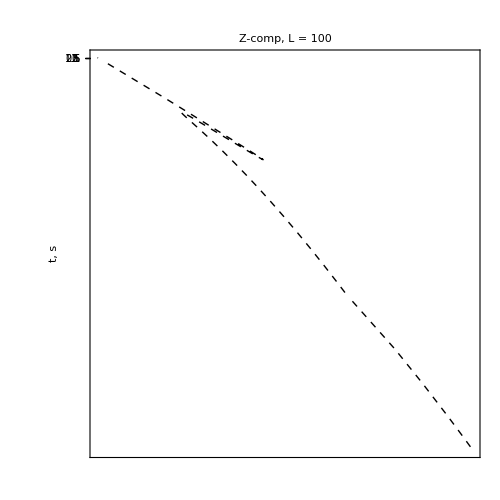
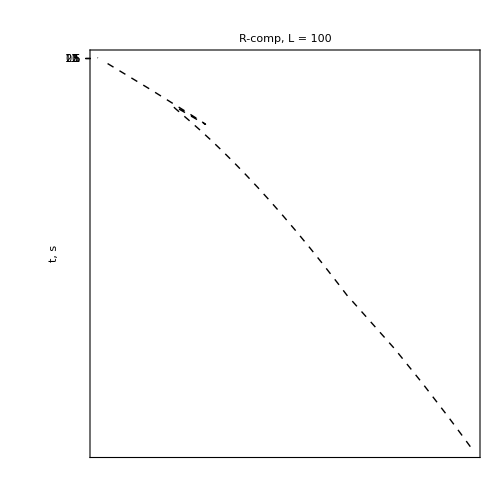
-Graphics--Graphics--Graphics- | -Graphics--Graphics--Graphics-

```mathematica
{{tlPlotSeismic[ToString@Row[{"Z-comp, L = ",L[[1]]}],L100[[;;,1,;;]],freqvec,x,15,Abs@ωI,layers,depth,{.4,.8},l100Z,50,2,"1S2PP1P"],
tlPlotSeismic[ToString@Row[{"R-comp, L = ",L[[1]]}],L100[[;;,2,;;]],freqvec,x,15,Abs@ωI,layers,depth,{.4,.8},l100R,50,2,"1S2PS1P"]}}//TableForm
```

{data, t} written to l200Z

{data, t} written to l200R

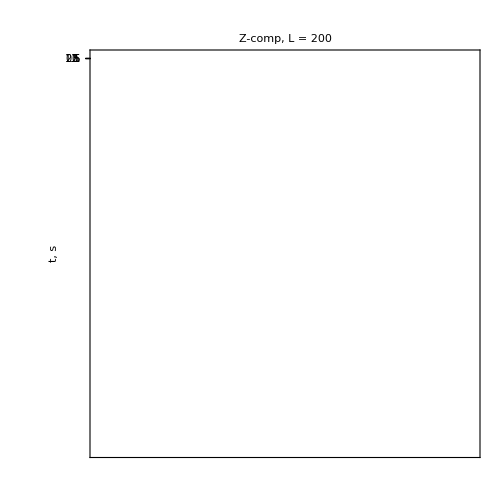
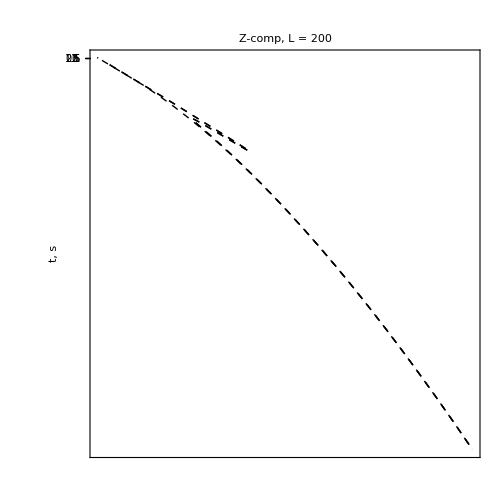
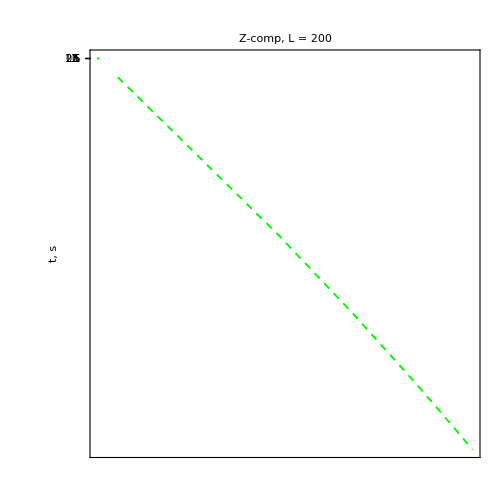
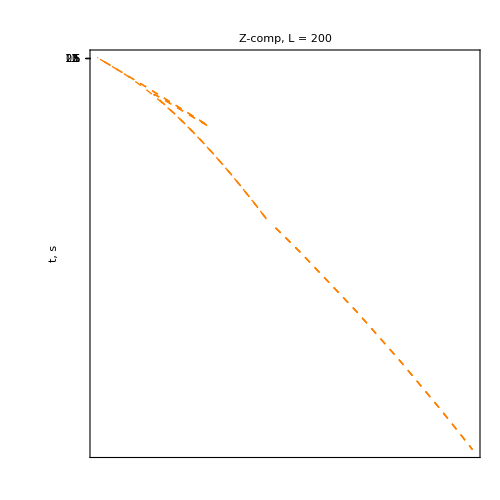
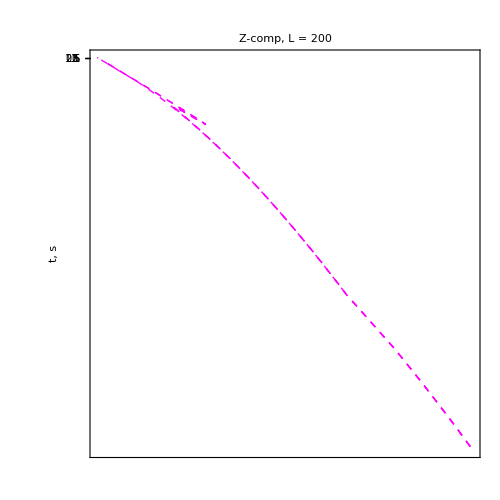
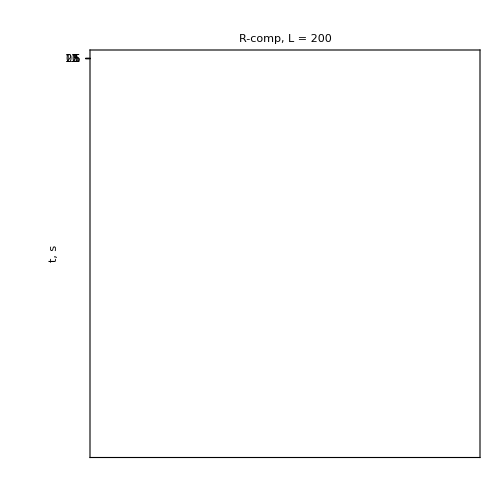
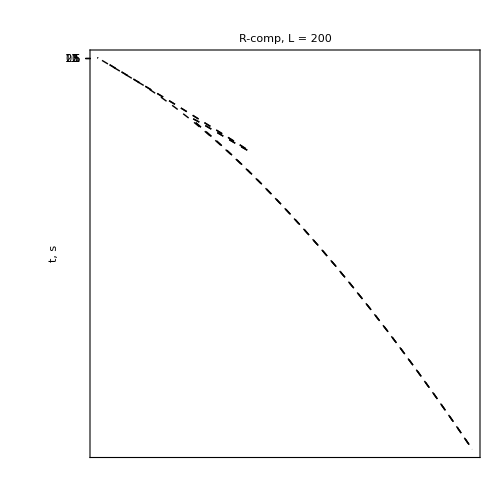
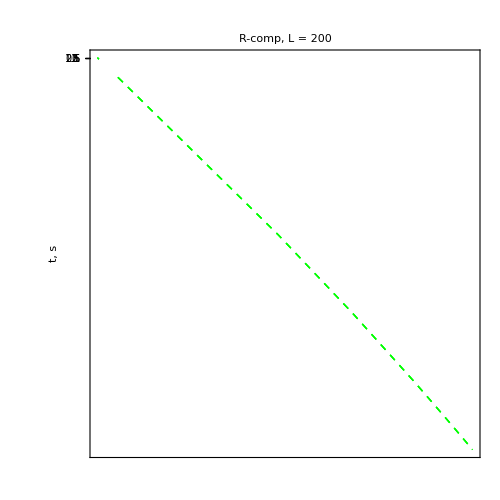
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics- | -Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
{{tlPlotSeismic[ToString@Row[{"Z-comp, L = ",L[[2]]}],L200[[;;,1,;;]],freqvec,x,1,Abs@ωI,layers,depth,{.4,.8},l200Z,50,2],
tlPlotSeismic[ToString@Row[{"R-comp, L = ",L[[2]]}],L200[[;;,2,;;]],freqvec,x,1,Abs@ωI,layers,depth,{.4,.8},l200R,50,2]}}//TableForm
```

{data, t} written to l300Z

{data, t} written to l300R

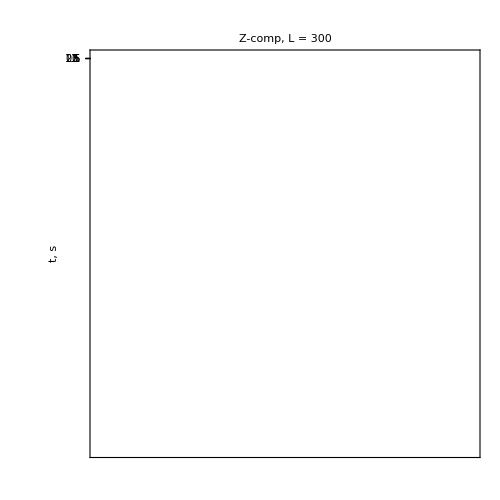
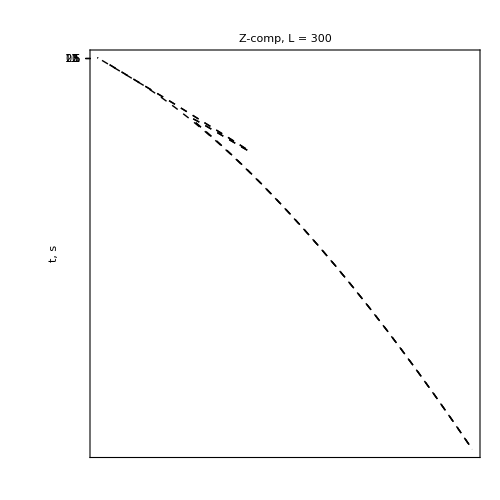
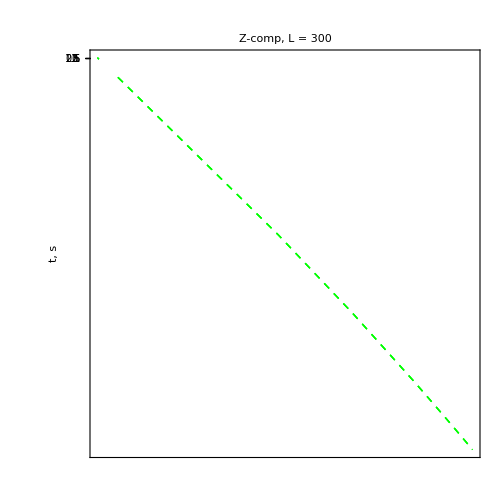
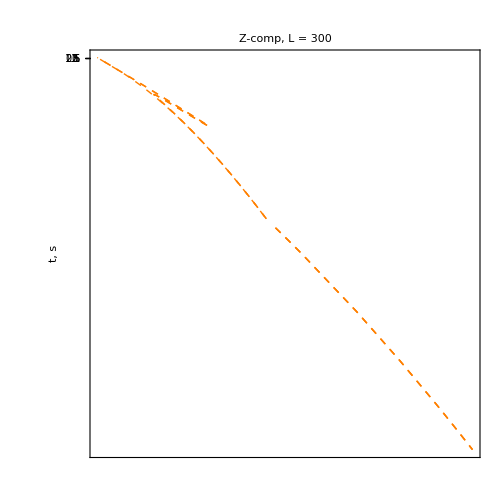
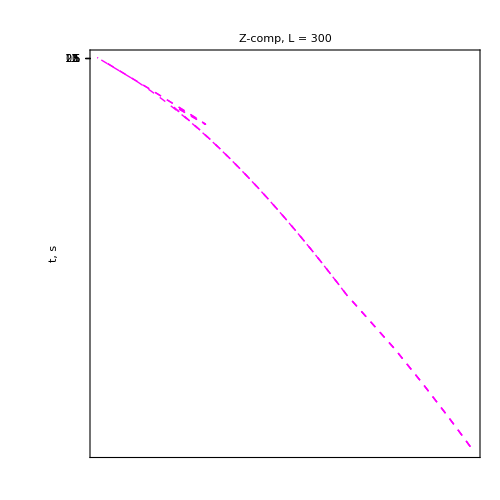
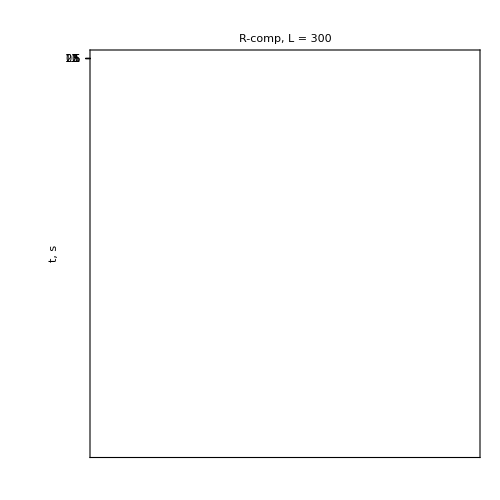
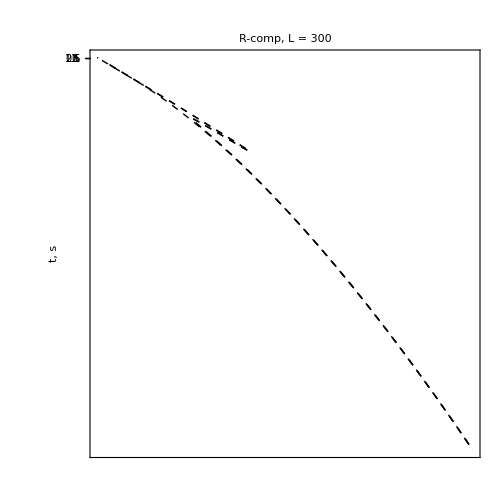
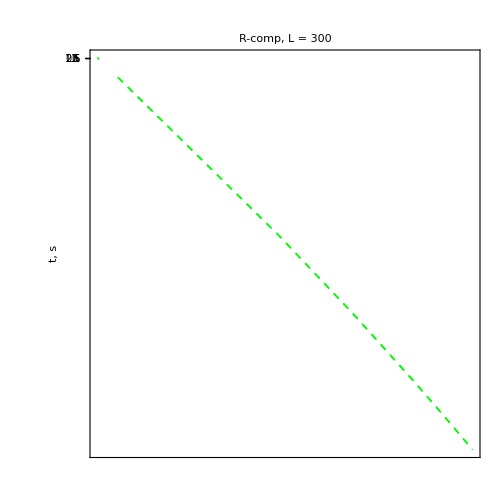
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics- | -Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
{{tlPlotSeismic[ToString@Row[{"Z-comp, L = ",L[[3]]}],L300[[;;,1,;;]],freqvec,x,1,Abs@ωI,layers,depth,{.4,.8},l300Z,50,2],
tlPlotSeismic[ToString@Row[{"R-comp, L = ",L[[3]]}],L300[[;;,2,;;]],freqvec,x,1,Abs@ωI,layers,depth,{.4,.8},l300R,50,2]}}//TableForm
```

## Single traces 1 km

#### d = 0.5 km; L = 100/200/300

```mathematica
With[{i=91,is=750,lim={0.4,.81}},traces1={{Show[
tlPlotTrace[L100[[;;,1,i]],freqvec,Abs@ωI,Red,50,lim,is,"Z component, x = "<>ToString[x[[i]]]<>" km"],
tlPlotTrace[L200[[;;,1,i]],freqvec,Abs@ωI,Cyan,50,lim,is,None],
tlPlotTrace[L300[[;;,1,i]],freqvec,Abs@ωI,Magenta,50,lim,is,None],LabelStyle->Directive[Black,Bold,FontSize->20]],
Show[
tlPlotTrace[L100[[;;,2,i]],freqvec,Abs@ωI,Red,50,lim,is,"R component, x = "<>ToString[x[[i]]]<>" km"],
tlPlotTrace[L200[[;;,2,i]],freqvec,Abs@ωI,Cyan,50,lim,is,None],
tlPlotTrace[L300[[;;,2,i]],freqvec,Abs@ωI,Magenta,50,lim,is,None],LabelStyle->Directive[Black,Bold,FontSize->20]]}};]
```

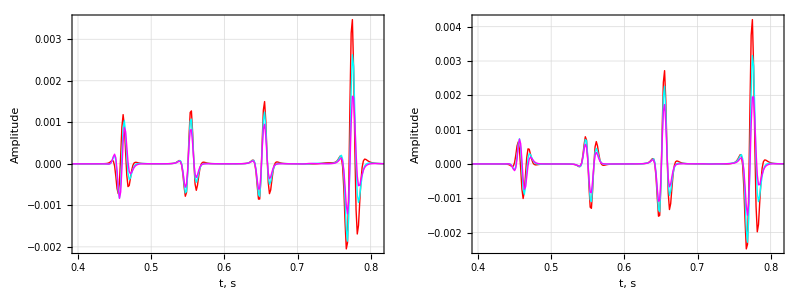

```mathematica
traces1//TableForm
```

```mathematica
With[{format=".eps"},
Table[Export[FigExportPath<>"traces-"<>Switch[i,1,"Z",2,"R"]<>format,traces1[[1,i]]],{i,2}];
]
```

```mathematica
With[{i=91,is=750,lim={0.81,1.3},prv=.0004{-1,1}},traces2={{Show[
tlPlotTrace[L100[[;;,1,i]],freqvec,Abs@ωI,Red,50,lim,is,"Z component, x = "<>ToString[x[[i]]]<>" km",prv],
tlPlotTrace[L200[[;;,1,i]],freqvec,Abs@ωI,Cyan,50,lim,is,None,prv],
tlPlotTrace[L300[[;;,1,i]],freqvec,Abs@ωI,Magenta,50,lim,is,None,prv],LabelStyle->Directive[Black,Bold,FontSize->20]],
Show[
tlPlotTrace[L100[[;;,2,i]],freqvec,Abs@ωI,Red,50,lim,is,"R component, x = "<>ToString[x[[i]]]<>" km",prv],
tlPlotTrace[L200[[;;,2,i]],freqvec,Abs@ωI,Cyan,50,lim,is,None,prv],
tlPlotTrace[L300[[;;,2,i]],freqvec,Abs@ωI,Magenta,50,lim,is,None,prv],LabelStyle->Directive[Black,Bold,FontSize->20]]}};]
```

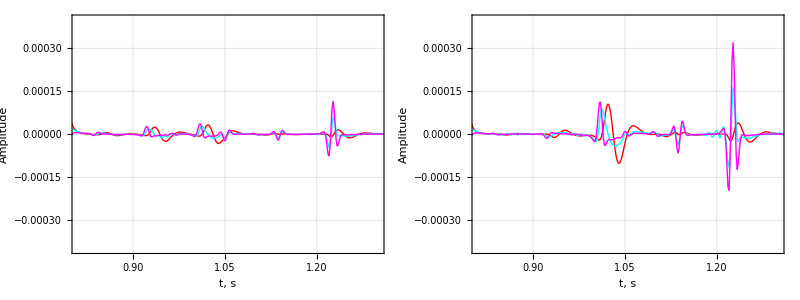

```mathematica
traces2//TableForm
```

```mathematica
With[{format=".eps"},
Table[Export[FigExportPath<>"tracesLate-"<>Switch[i,1,"Z",2,"R"]<>format,traces2[[1,i]]],{i,2}];
]
```

## Differences between CSG

```mathematica
With[{delta1=l100Z[[1]]-l300Z[[1]],delta2=l100R[[1]]-l300R[[1]]},
diff100300={{tlPlotDiff[ToString@Row[{"Z-comp, ΔL: ",L[[1]],", ",L[[3]]}],delta1,x,l100Z[[2]],1,{0.3,1.5},0,1/GoldenRatio],
tlPlotDiff[ToString@Row[{"R-comp, ΔL: ",L[[1]],", ",L[[3]]}],delta2,x,l100Z[[2]],1,{0.3,1.5},0,1/GoldenRatio]}}
]
```

{{-Graphics-,-Graphics-}}

```mathematica
With[{delta1=l100Z[[1]]-l200Z[[1]],delta2=l100R[[1]]-l200R[[1]]},
diff100200={{tlPlotDiff[ToString@Row[{"Z-comp, ΔL: ",L[[1]],", ",L[[2]]}],delta1,x,l100Z[[2]],1,{0.3,1.5},0,1/GoldenRatio],
tlPlotDiff[ToString@Row[{"R-comp, ΔL: ",L[[1]],", ",L[[2]]}],delta2,x,l100Z[[2]],1,{0.3,1.5},0,1/GoldenRatio]}}
]
```

{{-Graphics-,-Graphics-}}

```mathematica
With[{delta1=l200Z[[1]]-l300Z[[1]],delta2=l200R[[1]]-l300R[[1]]},
diff200300={{tlPlotDiff[ToString@Row[{"Z-comp, ΔL: ",L[[2]],", ",L[[3]]}],delta1,x,l100Z[[2]],1,{0.3,1.5},0,1/GoldenRatio],
tlPlotDiff[ToString@Row[{"R-comp, ΔL: ",L[[2]],", ",L[[3]]}],delta2,x,l100Z[[2]],1,{0.3,1.5},0,1/GoldenRatio]}}
]
```

{{-Graphics-,-Graphics-}}

```mathematica
With[{format=".eps"},
Table[
Table[
Export[FigExportPath<>"/diff-"<>Switch[i,1,"Z",2,"R"]<>Switch[j,1,"100300",2,"100200",3,"200300"]<>format,Switch[j,1,diff100300,2,diff100200,3,diff200300][[1,i]]],
{i,2}],{j,3}
];
]
```

## Shot gathers: N = 25

```mathematica
{freqvec,L100N25,pI,ωI,layersN25,depthN25}=Uncompress@Import[NotebookDirectory[]<>"./!l100n25d500.mc","String"];
{freqvec,L200N25,pI,ωI,layersN25,depthN25}=Uncompress@Import[NotebookDirectory[]<>"./!l200n25d500.mc","String"];
{freqvec,L300N25,pI,ωI,layersN25,depthN25}=Uncompress@Import[NotebookDirectory[]<>"./!l300n25d500.mc","String"];
```

{data, t} written to l100N25Z

{data, t} written to l100N25R

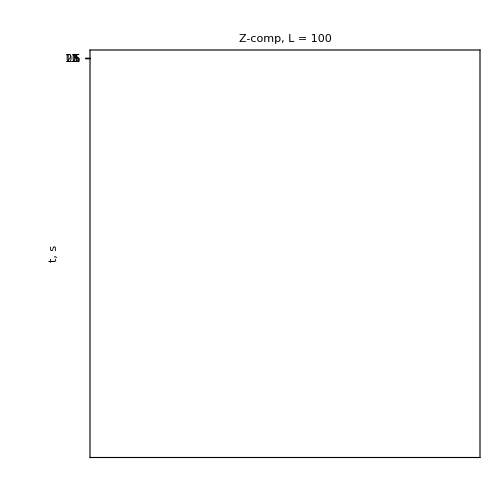
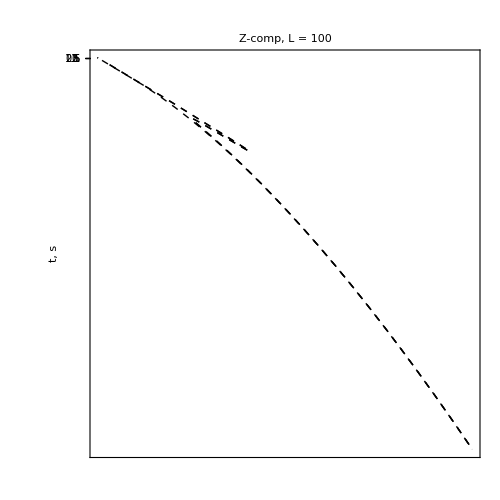
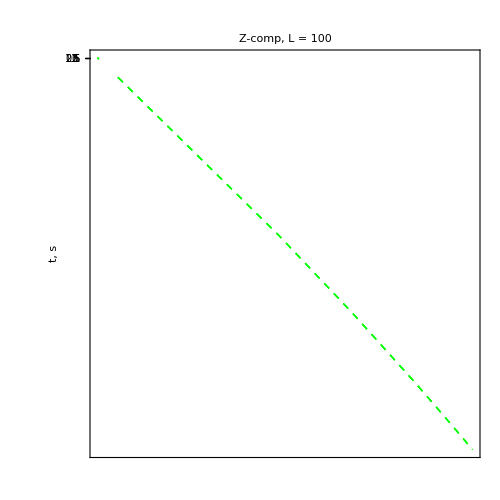
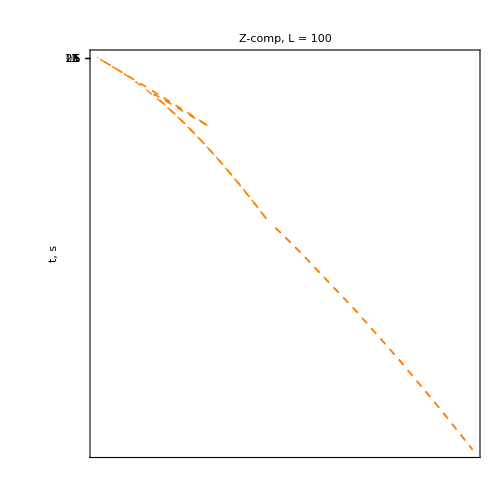
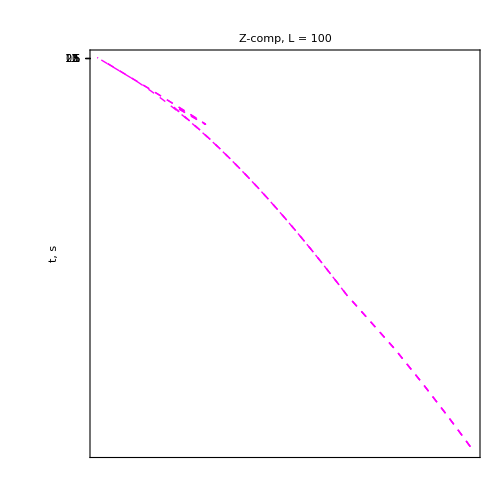
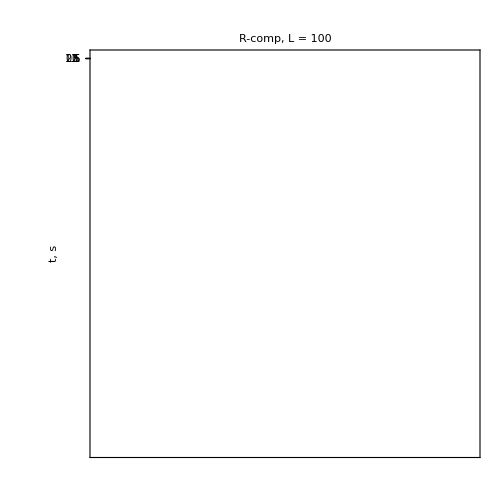
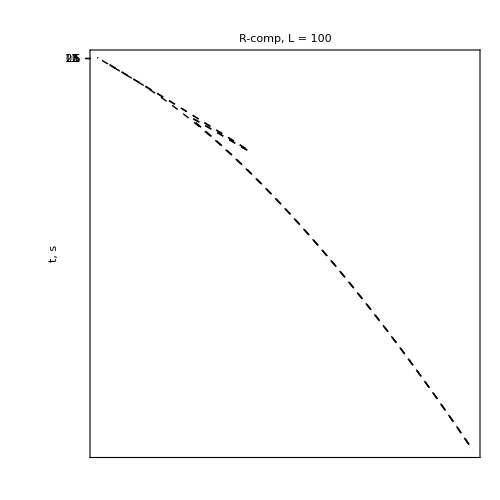
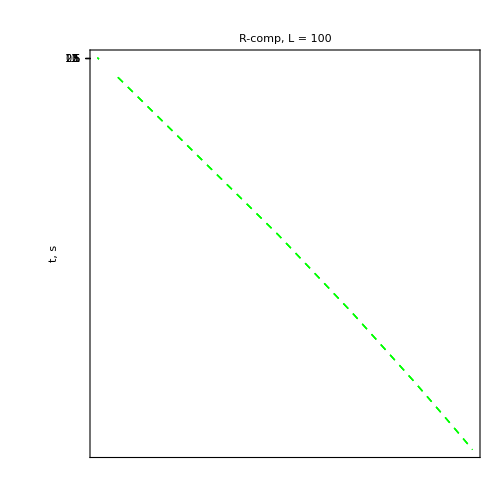
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics- | -Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
{{tlPlotSeismic[ToString@Row[{"Z-comp, L = ",L[[1]]}],L300N25[[;;,1,;;]],freqvec,x,1,Abs@ωI,layers,depth,{.4,.8},l100N25Z,25,2],
tlPlotSeismic[ToString@Row[{"R-comp, L = ",L[[1]]}],L300N25[[;;,2,;;]],freqvec,x,1,Abs@ωI,layers,depth,{.4,.8},l100N25R,25,2]}}//TableForm
```

```mathematica
With[{delta1=l100Z[[1]]-l100N25Z[[1]],delta2=l100R[[1]]-l100N25R[[1]]},
{tlPlotDiff[ToString@Row[{"Z-comp, ΔL: ",L[[1]],", ",L[[2]]}],delta1,x,l100Z[[2]],1,{0,2},0],
tlPlotDiff[ToString@Row[{"R-comp, ΔL: ",L[[1]],", ",L[[3]]}],delta2,x,l100Z[[2]],1,{0,2},0]}
]
```

{-Graphics-,-Graphics-}

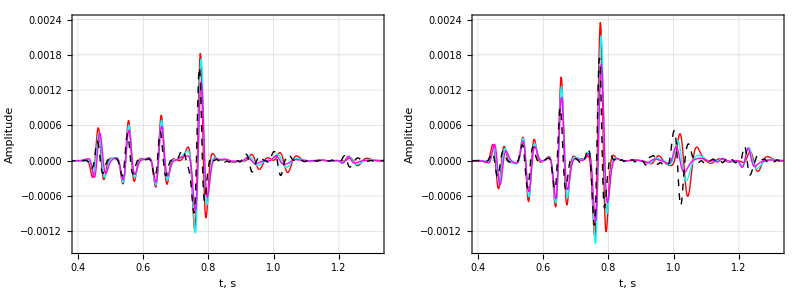

```mathematica
With[{i=91,is=750,lim={0.4,1.32},fR=20},tracesN25={{Show[
tlPlotTrace[L100[[;;,1,i]],freqvec,Abs@ωI,Red,fR,lim,is,"Z component, x = "<>ToString[x[[i]]]<>" km",{-.0015,.0024}],
tlPlotTrace[L200[[;;,1,i]],freqvec,Abs@ωI,Cyan,fR,lim,is,None],
tlPlotTrace[L300[[;;,1,i]],freqvec,Abs@ωI,Magenta,fR,lim,is,None],
tlPlotTrace[L100N25[[;;,1,i]],freqvec,Abs@ωI,{Dashed,Black},fR,lim,is,None],LabelStyle->Directive[Black,Bold,FontSize->20]],
Show[
tlPlotTrace[L100[[;;,2,i]],freqvec,Abs@ωI,Red,fR,lim,is,"R component, x = "<>ToString[x[[i]]]<>" km",{-.0015,.0024}],
tlPlotTrace[L200[[;;,2,i]],freqvec,Abs@ωI,Cyan,fR,lim,is,None],
tlPlotTrace[L300[[;;,2,i]],freqvec,Abs@ωI,Magenta,fR,lim,is,None],
tlPlotTrace[L100N25[[;;,2,i]],freqvec,Abs@ωI,{Dashed,Black},fR,lim,is,None],LabelStyle->Directive[Black,Bold,FontSize->20]]}}
];
tracesN25//TableForm
```

```mathematica
With[{format=".eps"},
Table[Export[FigExportPath<>"traces25-"<>Switch[i,1,"Z",2,"R"]<>format,tracesN25[[1,i]]],{i,2}];
]
```

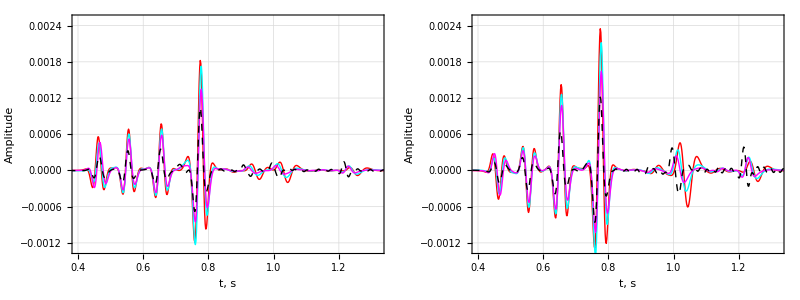

```mathematica
With[{i=91,is=750,lim={0.4,1.32}},tracesN25300={{Show[
tlPlotTrace[L100[[;;,1,i]],freqvec,Abs@ωI,Red,20,lim,is,"Z component, x = "<>ToString[x[[i]]]<>" km",{-.0013,.0025}],
tlPlotTrace[L200[[;;,1,i]],freqvec,Abs@ωI,Cyan,20,lim,is,None],
tlPlotTrace[L300[[;;,1,i]],freqvec,Abs@ωI,Magenta,20,lim,is,None],
tlPlotTrace[L300N25[[;;,1,i]],freqvec,Abs@ωI,{Dashed,Black},20,lim,is,None],LabelStyle->Directive[Black,Bold,FontSize->20]],
Show[
tlPlotTrace[L100[[;;,2,i]],freqvec,Abs@ωI,Red,20,lim,is,"R component, x = "<>ToString[x[[i]]]<>" km",{-.0013,.0025}],
tlPlotTrace[L200[[;;,2,i]],freqvec,Abs@ωI,Cyan,20,lim,is,None],
tlPlotTrace[L300[[;;,2,i]],freqvec,Abs@ωI,Magenta,20,lim,is,None],
tlPlotTrace[L300N25[[;;,2,i]],freqvec,Abs@ωI,{Dashed,Black},20,lim,is,None],LabelStyle->Directive[Black,Bold,FontSize->20]]}}
];
tracesN25300//TableForm
```

## 2-point ray tracing and plotting

```mathematica
RT[X0_,code_]:=Module[{X,P,p},
X[p_]:=tlTravelTimes[layers,depth,p,.4,.8,code][[1]];

P=NMinimize[{Abs[X[p]^2-X0^2],p≥0},p][[2,1,2]];

tlTravelTimes[layers,depth,P,.4,.8,code]
]
```

```mathematica
RT[1.0,"1P2PS1S"]
```

{1.,1.03969}

```mathematica
layers
```

{1,2,1}

```mathematica
codes={"1PP","1PS","1SP","1SS",
"1P2PP1P","1P2PS1P","1P2SS1P",
"1S2SS1S","1S2PS1S","1S2PP1S",

"1S2PP1P","1S2PS1P","1S2SS1P",
"1P2SS1S","1P2PS1S","1P2PP1S"
};
```

```mathematica
Table[
Module[{temp},
temp={tlPlotSeismic[ToString@Row[{"Z-comp, L = ",L[[3]]}],L300[[;;,1,;;]],freqvec,x,1,Abs@ωI,layers,depth,{.4,.8},0,50,2,codes[[i]]],
tlPlotSeismic[ToString@Row[{"R-comp, L = ",L[[3]]}],L300[[;;,2,;;]],freqvec,x,1,Abs@ωI,layers,depth,{.4,.8},0,50,2,codes[[i]]]};

With[{format=".eps"},
Export[FigExportPath<>"CSG-Z"<>ToString[i]<>format,temp[[1]]];
Export[FigExportPath<>"CSG-R"<>ToString[i]<>format,temp[[2]]];
];

];
,
{i,Length@codes}];
```

```mathematica
codes={"1PP","1S2SS1S"};
Table[

Module[{temp},
temp={
tlPlotSeismic[ToString@Row[{"Z-comp, L = ",L[[1]]}],L100N25[[;;,1,;;]],freqvec,x,1,Abs@ωI,layers,depth,{.4,.8},0,50,2,codes[[i]]],
tlPlotSeismic[ToString@Row[{"R-comp, L = ",L[[1]]}],L100N25[[;;,2,;;]],freqvec,x,1,Abs@ωI,layers,depth,{.4,.8},0,50,2,codes[[i]]]};

With[{format=".eps"},
Export[FigExportPath<>"CSGN25-Z"<>ToString[i]<>format,temp[[1]]];
Export[FigExportPath<>"CSGN25-R"<>ToString[i]<>format,temp[[2]]];
];

];
,
{i,Length@codes}];
```